```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 177 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,Parallel`Debug`Perfmon`,Parallel`Debug`,System`,Global`}

```mathematica
Clear[r]
r = { s[t] Cos[α] - 1/2 L Sin[θ[t]] , s[t] Sin[α] - 1/2 L Cos[θ[t]] }
```

{Cos[α] s[t]-1/2 L Sin[θ[t]],-1/2 L Cos[θ[t]]+s[t] Sin[α]}

```mathematica
D[r, t]
```

{Cos[α] s'[t]-1/2 L Cos[θ[t]] θ'[t],Sin[α] s'[t]+1/2 L Sin[θ[t]] θ'[t]}

```mathematica
D[r, t] . D[r, t]
```

(Cos[α] s'[t]-1/2 L Cos[θ[t]] θ'[t])^2+(Sin[α] s'[t]+1/2 L Sin[θ[t]] θ'[t])^2

```mathematica
D[r, t] . D[r, t]   // Expand
```

Cos[α]^2 s'[t]^2+Sin[α]^2 s'[t]^2-L Cos[α] Cos[θ[t]] s'[t] θ'[t]+L Sin[α] Sin[θ[t]] s'[t] θ'[t]+1/4 L^2 Cos[θ[t]]^2 θ'[t]^2+1/4 L^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[r, t] . D[r, t]   // Expand  //FullSimplify
```

s'[t]^2-L Cos[α+θ[t]] s'[t] θ'[t]+1/4 L^2 θ'[t]^2

```mathematica
Clear[T]
T = 1/2 M ( D[r, t] . D[r, t]   // Expand  //FullSimplify  ) +1/2(1/12 M L^2 θ'[t]^2)
```

1/24 L^2 M θ'[t]^2+1/2 M (s'[t]^2-L Cos[α+θ[t]] s'[t] θ'[t]+1/4 L^2 θ'[t]^2)

```mathematica
Clear[V]
V = 
M g r[[2]]
```

g M (-1/2 L Cos[θ[t]]+s[t] Sin[α])

```mathematica
Clear[ℒ]
ℒ = T - V ;
ℒ // pdConv
```

-g M (sin(α) s(t)-1/2 L cos(θ(t)))+1/2 M (1/4 L^2 ((∂θ(t))/(∂t))^2-L (∂s(t))/(∂t) (∂θ(t))/(∂t) cos(α+θ(t))+((∂s(t))/(∂t))^2)+1/24 L^2 M ((∂θ(t))/(∂t))^2

```mathematica
Clear[q]
q = { s[t] , θ[t] }
```

{s[t],θ[t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ] , t ] - D[ ℒ , q[[1]] ] 
D[ D[ ℒ , D[q[[2]], t] ] , t ] - D[ ℒ , q[[2]] ]  // Expand // Simplify
```

g M Sin[α]+1/2 M (L Sin[α+θ[t]] θ'[t]^2+2 s''[t]-L Cos[α+θ[t]] θ''[t])

1/6 L M (3 g Sin[θ[t]]-3 Cos[α+θ[t]] s''[t]+2 L θ''[t])

```mathematica
Table[
D[ ℒ , D[q[[i]], t] ] - D[ ℒ , q[[i]] ] ,
{ i , 1 , 2 } ] // TableForm
```

g M Sin[α]+1/2 M (2 s'[t]-L Cos[α+θ[t]] θ'[t])
1/2 g L M Sin[θ[t]]+1/12 L^2 M θ'[t]-1/2 L M Sin[α+θ[t]] s'[t] θ'[t]+1/2 M (-L Cos[α+θ[t]] s'[t]+1/2 L^2 θ'[t])

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

-1/2 M (2 g Sin[α]+L Sin[α+θ[t]] θ'[t]^2+2 s''[t]-L Cos[α+θ[t]] θ''[t])==0
-1/6 L M (3 g Sin[θ[t]]-3 Cos[α+θ[t]] s''[t]+2 L θ''[t])==0

```mathematica
Clear[parameters]
parameters = {
M-> 10 , 
g -> 9.8 ,
L-> 1 ,
α-> π/6
};
parameters // TableForm
```

M→10
g→9.8
L→1
α→π/6

```mathematica
eqs /. parameters // Expand // TableForm
```

-49.-5 Sin[π/6+θ[t]] θ'[t]^2-10 s''[t]+5 Cos[π/6+θ[t]] θ''[t]==0
-49. Sin[θ[t]]+5 Cos[π/6+θ[t]] s''[t]-(10 θ''[t])/3==0

```mathematica
Clear[ics]
ics = {
θ[0] == -0.1 ,
θ'[0] == 0 , 
s[0] == 0 ,
s'[0] == 0
} ;
ics // TableForm
```

θ[0]==-0.1
θ'[0]==0
s[0]==0
s'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[NDSolve[ Union[ eqs /. parameters , ics ] , q , { t , 0 , 10 } ] ]
```

{s[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t] ]  , { t , 0 , 10 }, PlotLabels-> { q[[1]] , q[[2]] }  ]
```

-Graphics-

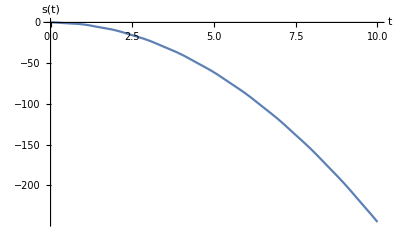

```mathematica
Plot[ q[[1]] /. solution[t] , { t , 0 , 10 } , AxesLabel-> { t , q[[1]] }]
```

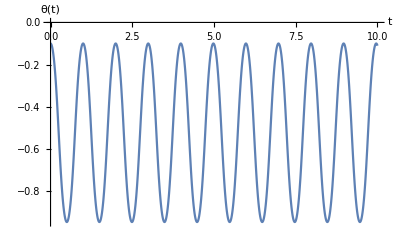

```mathematica
Plot[ q[[2]] /. solution[t] , { t , 0 , 10 } , AxesLabel-> { t , q[[2]] } ]
```

```mathematica
solution[t]
solution[t][[1]]
solution[t][[1,2]]
```

{s[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

s[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

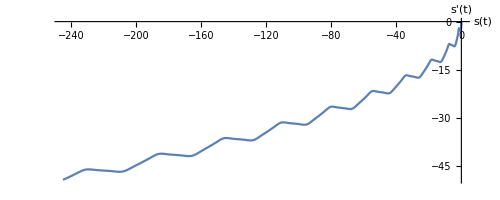

```mathematica
ParametricPlot[ {  solution[t][[1,2]] , solution'[t][[1,2]] } , { t, 0 , 10 } , AxesLabel-> { q[[1]]  , D[q[[1]], t] }  ]
```

```mathematica
solution[t]
solution[t][[2]]
solution[t][[2,2]]
```

{s[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

θ[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[
ParametricPlot[ {  solution[t][[2,2]] , solution'[t][[2,2]] } , { t, 0 , tmax } , AxesLabel-> { q[[2]]  , D[q[[2]], t] }  ]  , { tmax , 0.1 , 10 } ]
```

```mathematica
Animate[
ParametricPlot3D[ {  solution[t][[2,2]] , solution'[t][[2,2]] , t  } , { t , 0 , tmax } ]  ,
{ tmax , 0.1 , 10 } ]
```

```mathematica
eqs // TableForm
```

-1/2 M (2 g Sin[α]+L Sin[α+θ[t]] θ'[t]^2+2 s''[t]-L Cos[α+θ[t]] θ''[t])==0
-1/6 L M (3 g Sin[θ[t]]-3 Cos[α+θ[t]] s''[t]+2 L θ''[t])==0

```mathematica
Clear[translational]
translational = 
eqs //. θ'[t]-> 0 //. θ''[t] -> 0  ;
translational // TableForm
```

-1/2 M (2 g Sin[α]+2 s''[t])==0
-1/6 L M (3 g Sin[θ[t]]-3 Cos[α+θ[t]] s''[t])==0

```mathematica
Eliminate[ translational , s''[t] ]
```

-g L M Sin[θ[t]]==g L M Cos[α+θ[t]] Sin[α]

```mathematica
Solve[ 
Eliminate[ translational , s''[t] ]  , θ[t] ]  // FullSimplify  // PowerExpand
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ[t]→-ArcCos[-Cos[α]]},{θ[t]→ArcCos[-Cos[α]]},{θ[t]→-α},{θ[t]→α}}